## Eliminacion Transiciones Epsilon

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_]:=Graph[
edges,
VertexSize->0.55,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight"
]
```

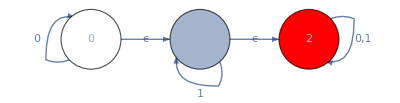

```mathematica
ShowGraphFA[{0->0,0->1,1->1,1->2,2->2},{0,1,2},{0},{2},{"0","ϵ","1","ϵ","0,1"}]
```

```mathematica
δ=Association[
{0,0}->{0},
{0,ϵ}->{1},
{1,ϵ}->{2},
{1,1}->{1},
{2,0}->{2},
{2,1}->{2}
];
```

Para este metodo es escencial la funcion de las clausuras Epsilon que usamos para los Epsilon AFN

```mathematica
Closure[δ_,state_List]:=Union[Map[Flatten[Most[NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}],{i,Length[#1]}]&,{#},!MissingQ[#]&]]]&,state]//Flatten]
```

```mathematica
Closure[δ,{0}]
```

{0,1,2}

Luego hay que montar la tabla, que es muy parecido al metodo de subconuntos para pasar de AFN a AFD, creamos como las filas y columnas de la tabla pero no la hemos llenado

```mathematica
states = {0,1,2}
```

{0,1,2}

```mathematica
(* Con esto tenemos la forma de la tabla, se hace cada "estado" por 0 y 1 (el alfabeto) creando la tabla que se hace a mano*)
```

```mathematica
newKeys = Outer[{#1,#2}&,states,{0,1},1]
```

{{{0,0},{0,1}},{{1,0},{1,1}},{{2,0},{2,1}}}

Para este metodo es importante sacar la clausura  epsilon de los estados

```mathematica
epsilonClosures = Association[{0} -> Closure[δ,{0}],  {1} -> Closure[δ,{1}], {2} -> Closure[δ,{2}]]
```

<|{0}→{0,1,2},{1}→{1,2},{2}→{2}|>

```mathematica
epsilonClosures[{0}]
```

{0,1,2}

Definimos la funcion delta hat epsilon

```mathematica
DeltaHatEpsilon[δ_,q0_List,string_]:=FoldList[Closure[δ,Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]]&,Closure[δ,q0],Characters[string]]
```

```mathematica
DeltaHatEpsilon[δ ,{0}, "0"]
```

{{0,1,2},{}}

```mathematica
(* Ahora debemos evaluar delta para cada row * col (sería como llenar la tabla) *)
```

```mathematica
Union[{DeltaHatEpsilon[δ ,{0}, "0"],DeltaHatEpsilon[δ ,{1}, "0"],DeltaHatEpsilon[δ ,{2}, "0"]}]/.{}->Nothing
```

{{{2}},{{1,2}},{{0,1,2}}}